### Constants

```mathematica
h = 6.626*10^(-34); (*J s*)
hbar = h/(2π);
e=-1.602*10^(-19); (* C *)
ϵ0=8.854*10^(-12); (* C^2/(J m) *)
me=9.109*10^(-31); (*kg*)
mp=1.673*10^(-27); (*kg*)
μ=(mp/(me+mp))*me;
a0=(4π ϵ0 hbar^2)/(μ e^2);
```

### Bohr hydrogen energies

```mathematica
Ens=Table[-hbar^2/(a0^2 2 μ n^2)*1/(1.602*10^(-19)),{n,1,10}]
```

{-13.5941,-3.39852,-1.51045,-0.84963,-0.543763,-0.377613,-0.27743,-0.212408,-0.167828,-0.135941}

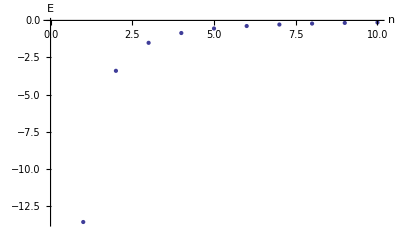

```mathematica
ListPlot[Ens, PlotRange->Full,AxesLabel->{"n", "E"}]
```

### Hydrogen Wave Functions

```mathematica
?LaguerreL
```

LaguerreL[n,x] gives the Laguerre polynomial L_n(x). 
LaguerreL[n,a,x] gives the generalized Laguerre polynomial L_n^a(x).

```mathematica
psi[n_,ρ_]:=Sqrt[2/n^2]ⅇ^-(ρ/ n)*LaguerreL[n-1,1,2*ρ/n]
```

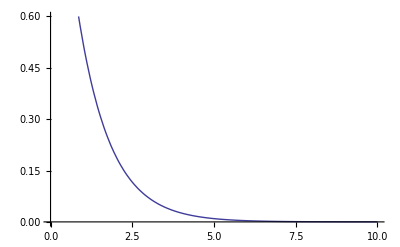

```mathematica
Plot[psi[1,r],{r,0,10}]
```

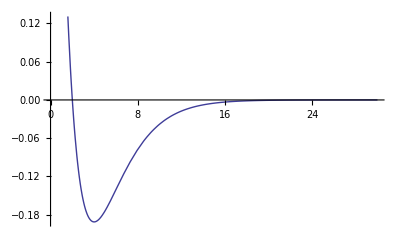

```mathematica
Plot[psi[2,r],{r,0,30}]
```

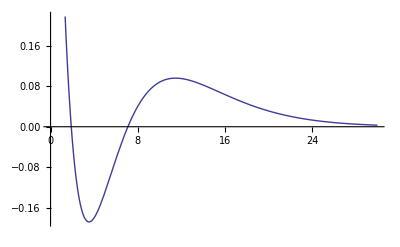

```mathematica
Plot[psi[3,r],{r,0,30}]
```

```mathematica
Integrate[psi[1,r]^2,{r,0,∞}]
```

1

```mathematica
Integrate[psi[2,r]^2,{r,0,∞}]
```

1

```mathematica
Integrate[psi[10,r]^2,{r,0,∞}]
```

1

#### test

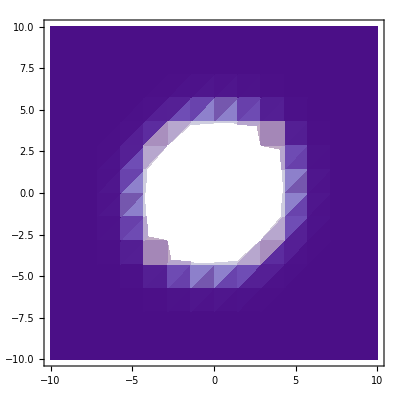
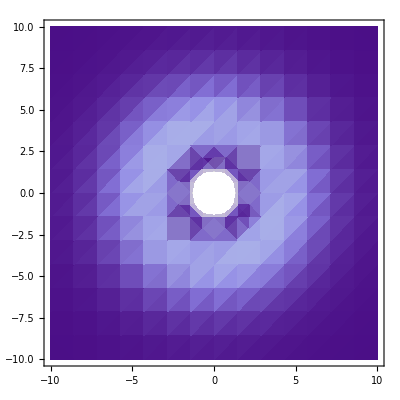
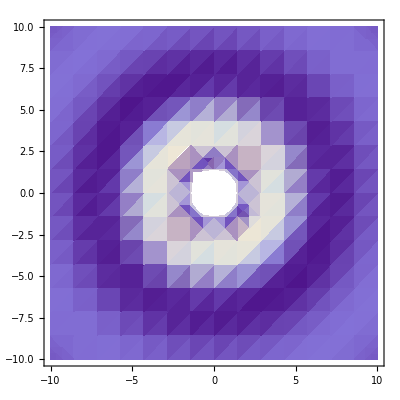
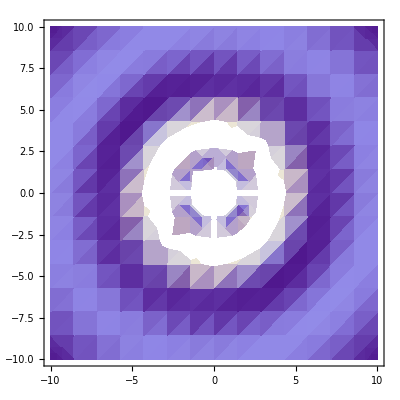
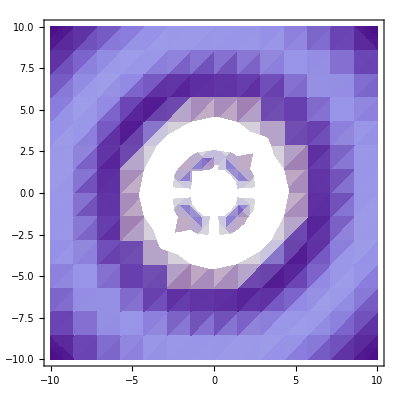
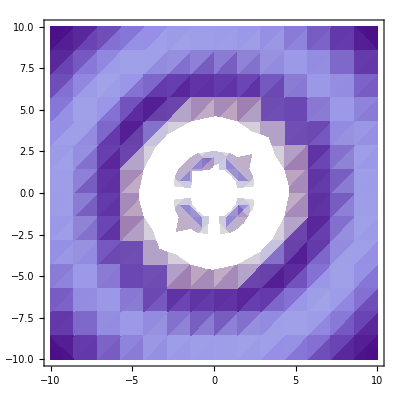

```mathematica
Table[DensityPlot[psi[n,Sqrt[x^2+y^2]]^2,{x,-10,10},{y,-10,10}],{n,1,6}]
```

#### actual file saving part

```mathematica
SetDirectory["~/Desktop/Ellen/Thesis/TeX/Thesis Template/Figures"]
```

/Network/Servers/Knowlton.local/Users/zphantom/Desktop/Ellen/Thesis/TeX/Thesis Template/Figures

```mathematica
Export["densityplots.png",Table[DensityPlot[psi[n,Sqrt[x^2+y^2]]^2,{x,-7,7},{y,-7,7}],{n,1,6}]]
```

densityplots.png

### Hydrogen V_eff

```mathematica
V[r_]:=n^2/2*1/r^2 - 1/r
```

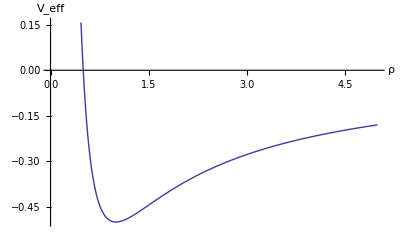

```mathematica
Plot[V[r]/.{n->1},{r,0,5},AxesLabel->{"ρ","V_eff"}]
```

### Yukawa Cutoff

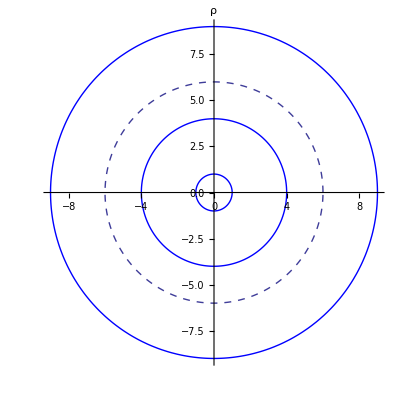

```mathematica
Show[PolarPlot[{1,4,9},{th,0,2π},PlotStyle->Blue,AxesLabel->"ρ"],PolarPlot[6,{th,0,2π},PlotStyle->Dashed]]
```

### Yukawa Veff

```mathematica
V[r_]:=n^2/2*1/r^2 - 1/r*ⅇ^(-r/l)
```

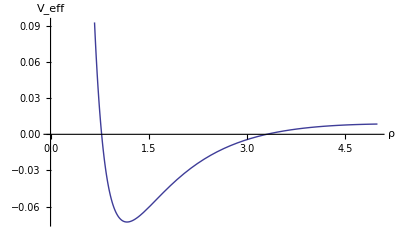

```mathematica
Plot[V[r]/.{n->1,l->1.75},{r,0,5},AxesLabel->{"ρ","V_eff"}]
```

### Numeric wave functions

```mathematica
Hyd=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
hvalvecs=Eigensystem[Hyd,-100];
```

```mathematica
sorted=Sort[hvalvecs[[1]]]
```

{-0.997512,-0.249844,-0.11108,-0.0624902,-0.039996,-0.0277758,-0.0204071,-0.0156244,-0.0123453,-0.00999353,-0.00811277,-0.00608617,-0.00360755,-0.000686981,0.00263874,0.00634558,0.0104176,0.0148435,0.019615,0.0247254,0.0301698,0.0359438,0.0420441,0.0484677,0.0552122,0.0622753,0.0696554,0.0773506,0.0853597,0.0936812,0.102314,0.111258,0.12051,0.130072,0.139941,0.150117,0.1606,0.171389,0.182484,0.193883,0.205586,0.217594,0.229905,0.24252,0.255437,0.268657,0.282179,0.296003,0.310129,0.324556,0.339284,0.354314,0.369644,0.385274,0.401205,0.417436,0.433966,0.450797,0.467927,0.485356,0.503085,0.521112,0.539439,0.558065,0.576989,0.596211,0.615732,0.635552,0.655669,0.676085,0.696798,0.71781,0.739119,0.760725,0.782629,0.804831,0.82733,0.850126,0.873219,0.896609,0.920296,0.94428,0.968561,0.993138,1.01801,1.04318,1.06865,1.09441,1.12047,1.14683,1.17348,1.20043,1.22767,1.25521,1.28305,1.31118,1.3396,1.36833,1.39734,1.42666}

```mathematica
Position[hvalvecs[[1]],sorted[[2]]]
```

{{58}}

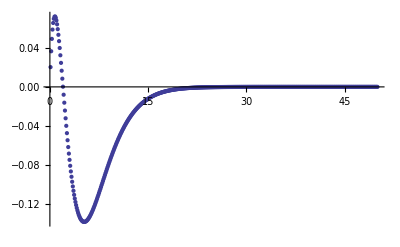

```mathematica
ListPlot[Table[{i/10, hvalvecs[[2,58,i]]},{i,1,500}],PlotRange->Full]
```

```mathematica
λ=200;
```

```mathematica
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
valvecs=Eigensystem[H,-100];
```

```mathematica
sorted=Sort[valvecs[[1]]]
```

{-0.00487541,-0.00301651,-0.00178452,-0.00097922,-0.000472414,-0.00017815,-0.0000359636,4.60923×10^-7,2.73965×10^-6,7.0553×10^-6,0.0000132512,0.0000212167,0.000030878,0.0000421828,0.0000550911,0.0000695714,0.0000855979,0.000103149,0.000122206,0.000142753,0.000164776,0.000188262,0.0002132,0.00023958,0.000267393,0.00029663,0.000327283,0.000359345,0.000392809,0.00042767,0.000463922,0.000501559,0.000540576,0.000580969,0.000622732,0.000665863,0.000710356,0.000756209,0.000803417,0.000851977,0.000901887,0.000953142,0.00100574,0.00105968,0.00111496,0.00117157,0.00122951,0.00128878,0.00134939,0.00141132,0.00147457,0.00153914,0.00160503,0.00167225,0.00174077,0.00181062,0.00188177,0.00195424,0.00202802,0.0021031,0.00217949,0.00225719,0.00233619,0.0024165,0.00249811,0.00258101,0.00266522,0.00275072,0.00283752,0.00292562,0.00301501,0.00310569,0.00319767,0.00329094,0.0033855,0.00348135,0.00357849,0.00367692,0.00377663,0.00387763,0.00397992,0.00408349,0.00418834,0.00429448,0.0044019,0.0045106,0.00462058,0.00473185,0.00484439,0.00495821,0.00507331,0.00518969,0.00530735,0.00542628,0.00554649,0.00566797,0.00579073,0.00591476,0.00604007,0.00616665}

```mathematica
Position[valvecs[[1]],sorted[[1]]]
```

{{12}}

```mathematica
Table[{i,1./i^2},{i,1,20}]
```

{{1,1.},{2,0.25},{3,0.111111},{4,0.0625},{5,0.04},{6,0.0277778},{7,0.0204082},{8,0.015625},{9,0.0123457},{10,0.01},{11,0.00826446},{12,0.00694444},{13,0.00591716},{14,0.00510204},{15,0.00444444},{16,0.00390625},{17,0.00346021},{18,0.00308642},{19,0.00277008},{20,0.0025}}

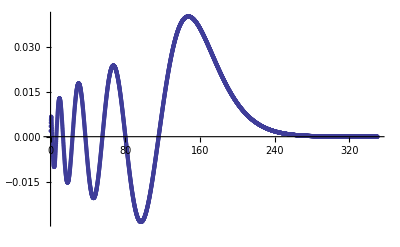

```mathematica
ListPlot[Table[{i/10, valvecs[[2,12,i]]},{i,1,3500}]]
```

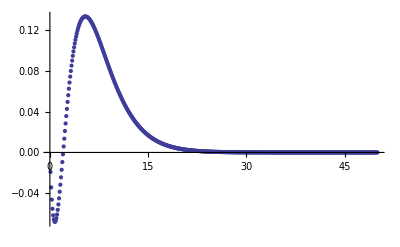

```mathematica
ListPlot[Table[{i/10, valvecs[[2,72,i]]},{i,1,500}],PlotRange->Full]
```

#### A scattering state becomes a bound state

λ = 12.5 (scattering), ρinf = 20*λ

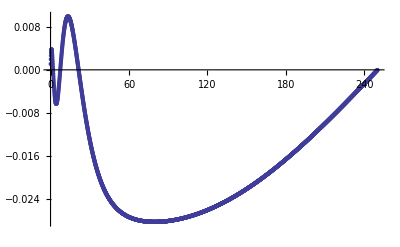

```mathematica
ListPlot[Table[{i/10, valvecs0[[2,100,i]]},{i,1,Length[valvecs0[[2,100]]]}]]
```

λ = 12.9 (scattering)

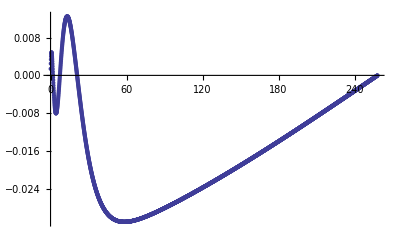

```mathematica
ListPlot[Table[{i/10, valvecs[[2,100,i]]},{i,1,Length[valvecs[[2,100]]]}]]
```

λ = 13.1 (bound)

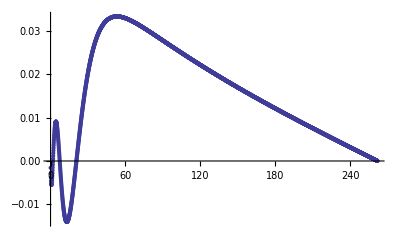

```mathematica
ListPlot[Table[{i/10, valvecs2[[2,100,i]]},{i,1,Length[valvecs2[[2,100]]]}]]
```

λ=14 (bound)

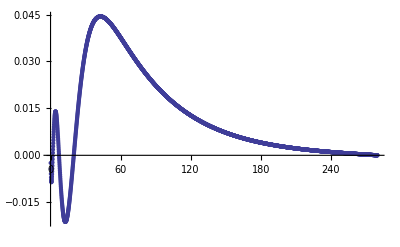

```mathematica
ListPlot[Table[{i/10, valvecs3[[2,99,i]]},{i,1,Length[valvecs3[[2,99]]]}]]
```

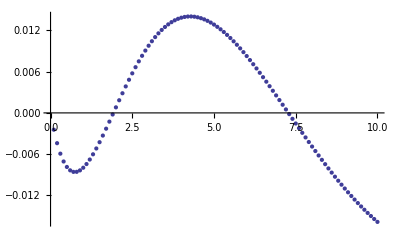

```mathematica
ListPlot[Table[{i/10, valvecs3[[2,99,i]]},{i,1,100}]]
```

#### The Importance of dρ

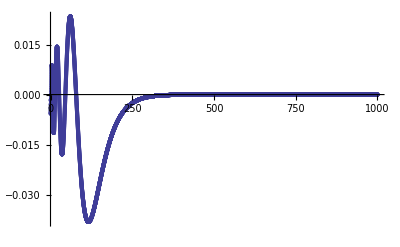

```mathematica
ListPlot[Table[{i/10, valvecs50[[2,93,i]]},{i,1,Length[valvecs50[[2,93]]]}],PlotRange->Full]
```

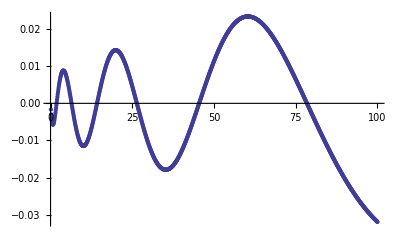

```mathematica
ListPlot[Table[{i/10, valvecs50[[2,93,i]]},{i,1,1000}]]
```

#### The Importance of ρinf

12.5, scattering

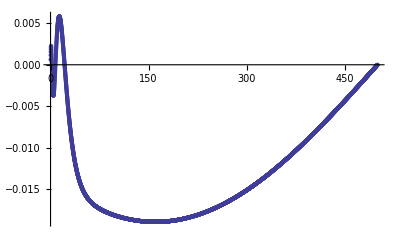

```mathematica
ListPlot[Table[{i/10, bigvalvecs0[[2,100,i]]},{i,1,Length[bigvalvecs0[[2,100]]]}]]
```

12.9, *bound*

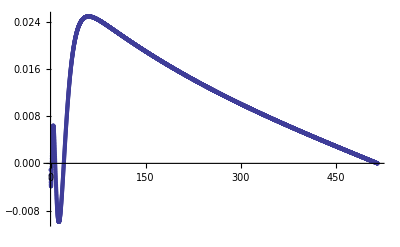

```mathematica
ListPlot[Table[{i/10, bigvalvecs[[2,100,i]]},{i,1,Length[bigvalvecs[[2,100]]]}]]
```

#### Plots for old things (λ=10)

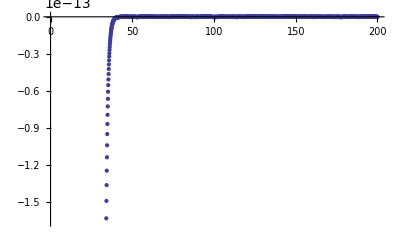

```mathematica
ListPlot[Table[{i/10, valvecs[[2,43,i]]},{i,1,Length[valvecs[[2,43]]]}]]
```

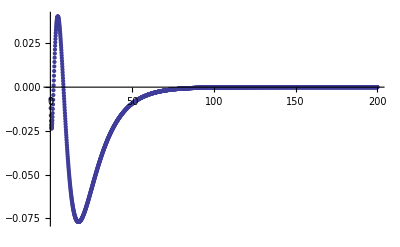

```mathematica
ListPlot[Table[{i/10, valvecs[[2,96,i]]},{i,1,Length[valvecs[[2,96]]]}],PlotRange->Full]
```

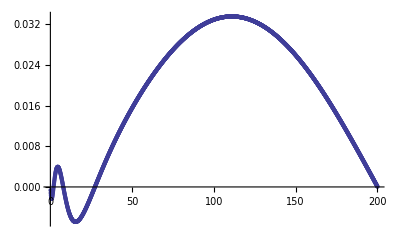

```mathematica
ListPlot[Table[{i/10, valvecs[[2,100,i]]},{i,1,Length[valvecs[[2,100]]]}],PlotRange->Full]
```